### 基本閉路行列の関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
Pin={{0,0},{1,2},{2,0.5},{3.5,3.5},{5,0}}(*Point input*)
```

{{0,0},{1,2},{2,0.5},{3.5,3.5},{5,0}}

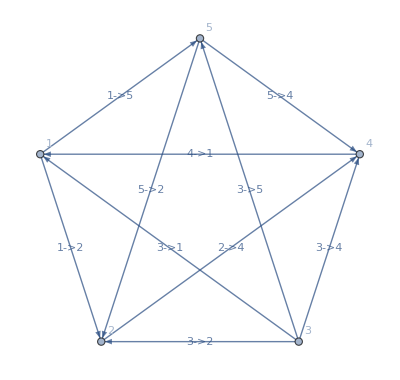

```mathematica
Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Random"](*Ggraph input*)
```

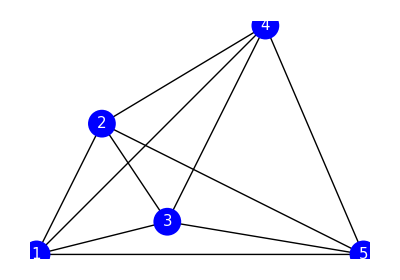

```mathematica
Graphics[{Thick,Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gin]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[StyleForm[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]
}]
```

```mathematica
Graphics[{Thick,Line[Table[
{Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gin]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[StyleForm[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]
}]
```

-Graphics-

```mathematica
h=LoopMatrix[Gin]
```

{{0,0,-1,-1,0,0,0,0,0,-1},{0,-1,0,-1,0,0,0,0,1,0},{0,-1,1,0,0,0,0,1,0,0},{1,0,1,0,0,1,0,0,0,0},{1,0,0,-1,0,0,-1,0,0,0},{1,1,0,0,-1,0,0,0,0,0}}

```mathematica
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}](* Point Distance *)
```

{√5,2.06155,4.94975,5,1.80278,2.91548,2 √5,3.3541,3.04138,3.80789}

```mathematica
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD
```

{{√5,0,0,0,0,0,0,0,0,0},{0.,2.06155,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,4.94975,0.,0.,0.,0.,0.,0.,0.},{0,0,0,5,0,0,0,0,0,0},{0.,0.,0.,0.,1.80278,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.91548,0.,0.,0.,0.},{0,0,0,0,0,0,2 √5,0,0,0},{0.,0.,0.,0.,0.,0.,0.,3.3541,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,3.04138,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,3.80789}}

```mathematica
s=Table[0,{i,Length[EdgeRules[Gin]]}]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
FLP=Table[
Pin[[
ConnectedComponents[FundLoop[[i]]][[1]]
]],
{i,Length[FundLoop]}](* Fundamental Loop Point *)
```

{{{5,0},{0,0},{3.5,3.5}},{{5,0},{0,0},{2,0.5}},{{3.5,3.5},{0,0},{2,0.5}},{{3.5,3.5},{0,0},{1,2}},{{5,0},{0,0},{1,2}},{{2,0.5},{0,0},{1,2}}}

```mathematica
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}<0,1,-1],
{i,Length[FundLoop]}](* 右回りならば正、左回りならば負 *)
```

{1,1,-1,1,1,1}

```mathematica
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[FundLoop[[i]]][[1]]]]
]],
{i,Length[FundLoop]}](* Fundamental Loop Area *)
```

{8.75,1.25,2.625,1.75,5,1.75}

```mathematica
U=Table[-LoopSpin[[i]]FLA[[i]],{i,Length[FundLoop]}](* 誘導起電力行列(誘導起電力は-B'Sに右回りなら1を、左回りなら-1をかける) *)
```

{-8.75,-1.25,2.625,-1.75,-5,-1.75}

```mathematica
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U)(* 誘導起電力行列を考慮した電流を求める式 *)
```

{-0.623285,-0.32532,0.348797,0.646762,-0.174382,-0.714377,0.0832895,0.0679409,0.43176,0.995233}

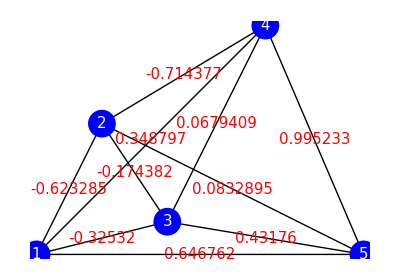

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gin]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[StyleForm[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[StyleForm[Curr[[i]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}]
```

```mathematica
Sort[Abs[Curr],Greater]
```

{0.995233,0.714377,0.646762,0.623285,0.43176,0.348797,0.32532,0.174382,0.0832895,0.0679409}

```mathematica
FindShortestTour[Pin]
```

{14.0624,{1,3,5,4,2,1}}

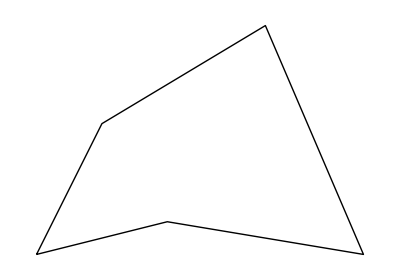

```mathematica
Graphics[Line[Pin[[Last[%]]]]]
```

```mathematica
ArrowList=Arrow[Table[If[Curr[[i]]>0,
{Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]]},
{Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]],Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]}
],{i,Length[EdgeRules[Gin]]}
]]
```

Arrow[{{{1,2},{0,0}},{{0,0},{2,0.5}},{{3.5,3.5},{0,0}},{{0,0},{5,0}},{{1,2},{2,0.5}},{{3.5,3.5},{1,2}},{{5,0},{1,2}},{{2,0.5},{3.5,3.5}},{{2,0.5},{5,0}},{{5,0},{3.5,3.5}}}]

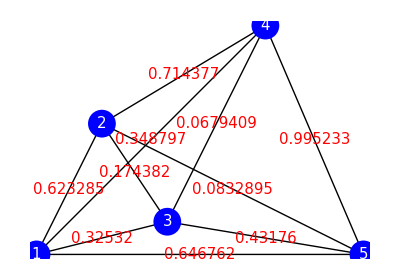

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],ArrowList,
Blue,PointSize[0.05],Point[Pin],White,Table[Text[StyleForm[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[StyleForm[Abs[Curr[[i]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
},PlotRange->All]
```

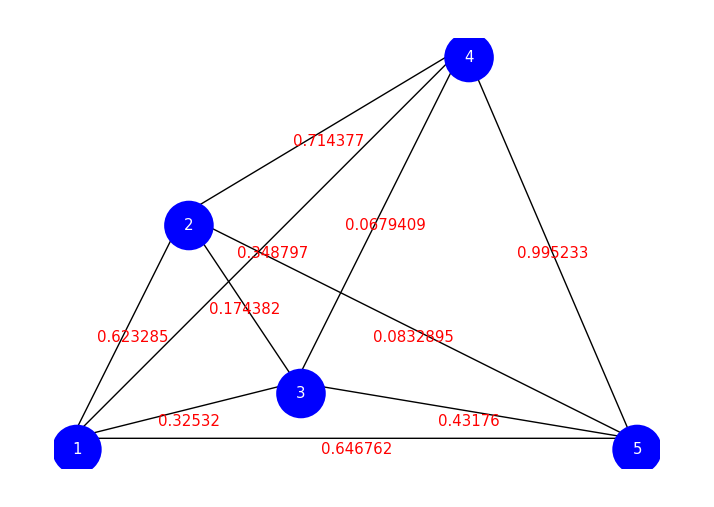

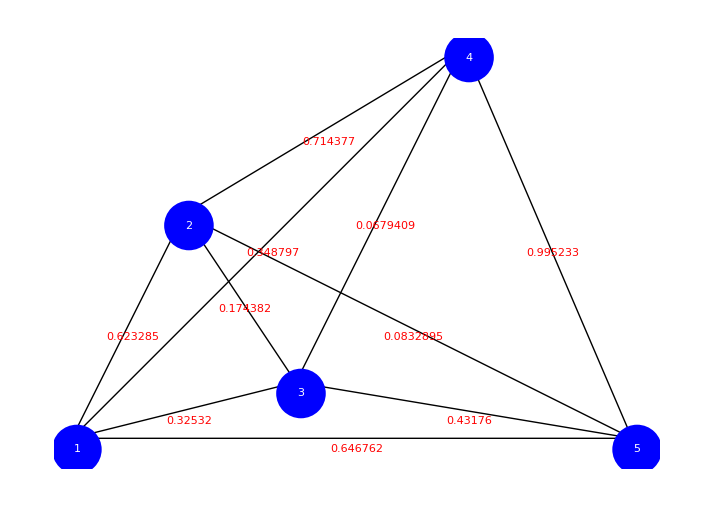

```mathematica
Gout=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

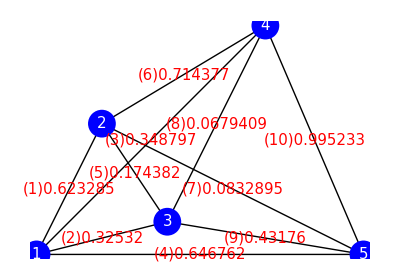

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[Abs[Curr[[i]]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```